# Fourier Sine Series

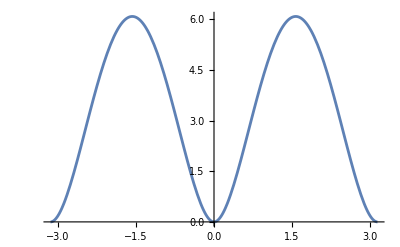

```mathematica
f[x_]:=x^2(π-x)^2
Show[
Plot[f[x],{x,0,π}],
Plot[f[-x],{x,-π,0}],
PlotRange->All
]
```

```mathematica
Integrate[f[x] Sin[n x],{x,0,π}]
```

(2 (-12+n^2 π^2) (-1+Cos[n π])-12 n π Sin[n π])/n^5

```mathematica
Simplify[ Integrate[f[x] Sin[n x],{x,0,π}],n∈Integers]
```

(2 (-1+(-1)^n) (-12+n^2 π^2))/n^5

```mathematica
Simplify[ Integrate[f[x] Sin[n x],{x,0,π}],Element[n,Integers]]
```

(2 (-1+(-1)^n) (-12+n^2 π^2))/n^5